```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/akcays/Desktop/BNS_work

## LIGO L1,H1 STRAIN during GW170817 and Interpolations

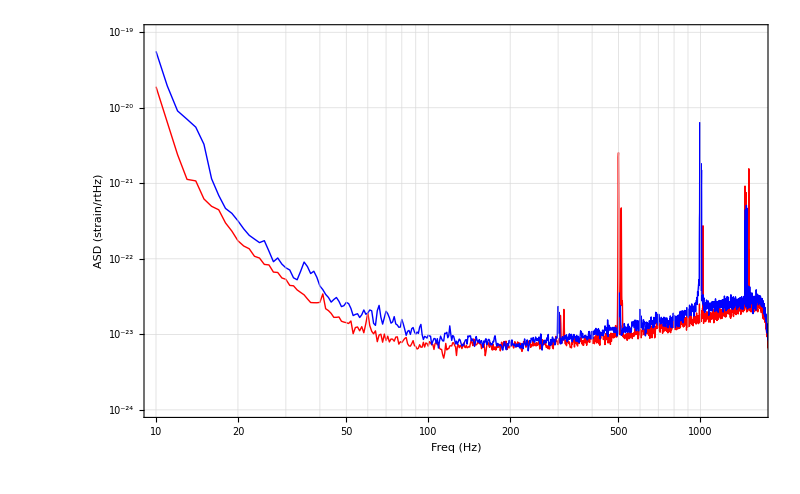

```mathematica
L1data="L-L1_LOSC_CLN_4_V1-1187007040-2048.hdf5";
H1data="H-H1_LOSC_CLN_4_V1-1187007040-2048.hdf5";
L1strain=SetPrecision[Import[L1data,{"Datasets","/strain/Strain"}],16];
H1strain=SetPrecision[Import[H1data,{"Datasets","/strain/Strain"}],16];
dt=1/4096;
(*L1attributes=Import[L1data,{"Attributes","/strain/Strain"}]
{t0,dtfloat,n}={"Xstart","Xspacing","Npoints"}/.L1attributes

dt-dtfloat
time=t0+(Range[n]-1) dt;*)
HannWindowTable=Table[HannWindow[(i-2048.5`16)/4096],{i,1,4096}];
MeanHann=Mean[Abs[Fourier[HannWindowTable]]^2];
AOL1specHann=Mean[Table[Abs[Fourier[L1strain[[1+4096 n;;4096 (n+1)]] HannWindowTable]]^2,{n,0,31}]]/MeanHann;
AOH1specHann=Mean[Table[Abs[Fourier[H1strain[[1+4096 n;;4096 (n+1)]] HannWindowTable]]^2,{n,0,31}]]/MeanHann;
L1ASD=Table[{i,Sqrt[2 dt AOL1specHann[[i+1]]]},{i,10,2000}];
H1ASD=Table[{i,Sqrt[2 dt AOH1specHann[[i+1]]]},{i,10,2000}];
L1ASDfit=Interpolation[L1ASD];
H1ASDfit=Interpolation[H1ASD];
GW170817L1ASDPlot=ListLogLogPlot[{L1ASD,H1ASD},Joined->True,GridLines->Automatic,Frame->True,PlotStyle->{Red,Blue},FrameLabel->{"Freq (Hz)","ASD (strain/rtHz)"},PlotRange->{{10,1600},{10^-24,10^-19}},ImageSize->800]
```

## Preliminaries

```mathematica
Msun=1.989*10^30;
clight=299792458;
Ggrav=6.67*10^-11;
fISCO=c^3/(6^(3/2)π G M);
Mpc=10^6*360/(2π)*3600*149597870700.;
fISCOGW170817=Block[{G=6.67*10^-11,M=(2.74Msun),c=clight},fISCO]
```

1605.37

## FREQ-DOMAIN STRAIN H̃(f) RMS average

```mathematica
A=π^(-2/3)√(5/24);
hFDRMS[f_]=Block[{D=40Mpc,G=6.67*10^-11,Mc=(1.188Msun),c=clight},2/5 A c/D(G Mc/c^3)^(5/6)f^(-7/6)]
```

(9.00904×10^-22)/f^(7/6)

## DEFINE THE SNR

```mathematica
SNRL1RMS[fi_,ff_]:=(NIntegrate[4 hFDRMS[f]^2/(L1ASDfit[f])^2,{f,fi,ff}])^(1/2)
SNRH1RMS[fi_,ff_]:=(NIntegrate[4 hFDRMS[f]^2/(H1ASDfit[f])^2,{f,fi,ff}])^(1/2)
```

## LIGO2017 PLOT

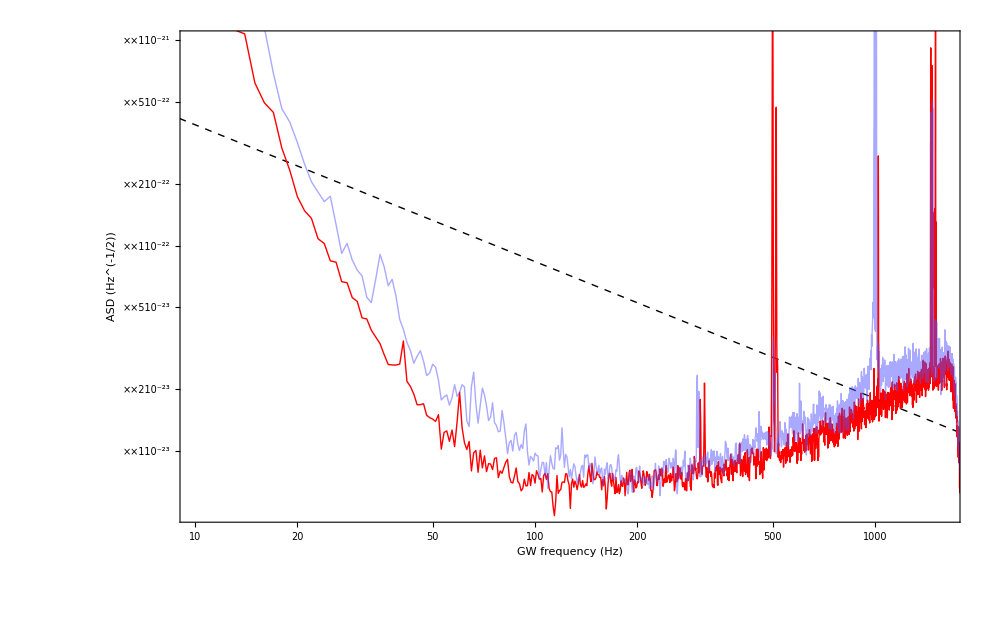

```mathematica
Show[LogLogPlot[{2 √f hFDRMS[f]},{f,1,2000},PlotStyle->{Black,Dashed,Thick},PlotRange->{{10,fISCOGW170817},{5 10^-24,10^-21}}],ListLogLogPlot[{L1ASD,H1ASD},Joined->True,PlotStyle->{Red,{Lighter[Blue],Opacity[0.5]}},AxesLabel->{"GW freq.",None},PlotRange->{All,All}],ImageSize->1000,
Frame->True,FrameStyle->Directive[Black,24,AbsoluteThickness[3]],FrameLabel->{Style["GW frequency (Hz)",24],Style["ASD (Hz^(-1/2))",24]}]
```

## Inspiral time, accumulated phase: 0PN to 3.5PN expressions

```mathematica
Tinsp0PN[f0_,Mch_]=5/(256 π^(8/3))  (c^3/(G Mch))^(5/3) f0^(-8/3)/.G->6.67*10^-11(*/.M->(2.8 Msun)*)/.c->clight;
Phi0PN[f0_,Mch_,M_]=2 (5 G Mch/c^3)^(-5/8) Tinsp0PN[f0,Mch]^(5/8)/.G->6.67*10^-11(*/.M->(2.8 Msun)*)/.c->clight;
Ncycles0PN[f0_,Mch_,M_]=1/(32 π^(8/3)) (G Mch/c^3)^(-5/3) (f0^(-5/3)-fISCO^(-5/3))/.G->6.67*10^-11(*/.M->(2.8 Msun)*)/.c->clight;
```

## CHECKS: GW170817 at LIGO 2017, use M = 2.74 M_Sun Swept from 30 Hz to~2000 Hz in 60 seconds and~3000 cycles with SNR=28.8 at L1

```mathematica
fin=30;
Print["τ_insp = ", Tinsp0PN[fin,1.188Msun] ," seconds"]
Print["𝒩_cyc  = ",Ncycles0PN[fin,1.188Msun,2.74Msun]," cycles"]
```

τ_insp = 55.9091 seconds

𝒩_cyc  = 2680.1 cycles

```mathematica
SNRL1=SNRL1RMS[fin,fISCOGW170817]//Quiet
SNRH1=SNRH1RMS[fin,fISCOGW170817]//Quiet
SNRtot=√(SNRL1^2+SNRH1^2)
```

14.2899

10.6476

17.8206

```mathematica
(*Note that our SNRs above are too low because we are using the RMS averaged one. 
MAximum SNR would be 5/2=2.5 times great because we'd simply remove the factor of 2/5 in H̃(f)*)
```

```mathematica
SNRL1max=2.5SNRL1RMS[fin,fISCOGW170817]//Quiet
SNRH1max=2.5SNRH1RMS[fin,fISCOGW170817]//Quiet
SNRtotMax=√(SNRL1max^2+SNRH1max^2)
```

35.7248

26.6191

44.5515

```mathematica
(*So we see that our RMS is too low for this event, and the Max, not surprisingly, is too high
The true SNRs are somewhere in between telling us that the event's sky location was actually on the luckier side*)
```